## Momenta diagrams

```mathematica
s=1/10{2,8};
t=1/10{-1,3};
```

```mathematica
ymin=-0.05;
ymax=0.85;
xmin=-0.4;
xmax=0.4;
```

```mathematica
p4=t+1/2{1,1}.(s-t){1,1}
p1=t+1/2{-1,1}.(s-t){-1,1}
```

{3/10,7/10}

{-1/5,2/5}

```mathematica
sx=s⟦1⟧;
tx=t⟦1⟧;
```

### s channel

```mathematica
qs=p4-{1,0}.(p4-s){1,1}
```

{1/5,3/5}

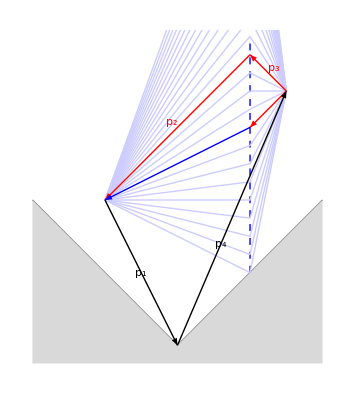

```mathematica
schannel=Graphics[{
Gray,
Line[{{xmin,-xmin},{0,0},{xmax,xmax}}],
LightGray,
Polygon[{{xmin,-xmin},{0,0},{xmax,xmax},{xmax,ymin},{xmin,ymin}}],
Blue,
Dashed,
Line[{{sx,Abs[sx]},{sx,ymax}}],
Dashing[None],
RGBColor[{0.8,0.8,1}],
Table[Line[{p4,{sx,y},p1}],{y,DeleteElements[Table[y,{y,sx,1.5,1/20}],{s[[2]],qs[[2]]}]}],
Black,Thick,
Arrow[{{0,0},p4}],
Arrow[{p1,{0,0}}],
Red,
Arrow[{p4,s}],
Arrow[{s,p1}],
Arrow[{p4,qs}],
Blue,
Arrow[{qs,p1}],
Black,
Text["p_4",0.4p4,{-2,0}],
Text["p_1",0.5p1,{2,0}],
Red,
Text["p_3",0.5p4+0.5s,1.5{-1,-1}],
Text["p_2",0.5p1+0.5s,1.5{1,-1}]
}//Flatten,PlotRange->{{xmin,xmax},{ymin,ymax}},BaseStyle->{FontSize->16,FontFamily->"Latin Modern Math"}]
```

### t channel

```mathematica
qt1=p4+{1,0}.(p4-t){-1,1}
qt2=p1-{1,0}.(p1-t){1,1}
```

{-1/10,11/10}

{-1/10,1/2}

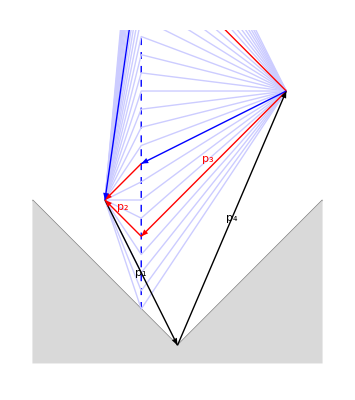

```mathematica
tchannel=Graphics[{
Gray,
Line[{{xmin,-xmin},{0,0},{xmax,xmax}}],
LightGray,
Polygon[{{xmin,-xmin},{0,0},{xmax,xmax},{xmax,ymin},{xmin,ymin}}],
Blue,
Dashed,
Line[{{tx,Abs[tx]},{tx,ymax}}],
Dashing[None],
RGBColor[{0.8,0.8,1}],
Table[Line[{p4,{tx,y},p1}],{y,DeleteElements[Table[y,{y,Abs[tx],1.5,1/20}],{t[[2]],qt1[[2]],qt2[[2]]}]}],
Black,Thick,
Arrow[{{0,0},p4}],
Arrow[{p1,{0,0}}],
Red,
Arrow[{p4,t}],
Arrow[{t,p1}],
Arrow[{p4,qt1}],
Arrow[{qt2,p1}],
Blue,
Arrow[{p4,qt2}],
Arrow[{qt1,p1}],
Black,
Text["p_4",0.5p4,{-2,0}],
Text["p_1",0.5p1,{2,0}],
Red,
Text["p_3",0.5p4+0.5t,1.5{1,-1}],
Text["p_2",0.66p1+0.34t,1.5{-1,-1}]
}//Flatten,PlotRange->{{xmin,xmax},{ymin,ymax}},BaseStyle->{FontSize->16,FontFamily->"Latin Modern Math"}]
```

### Regular case

```mathematica
(*qx=(sx+tx)/2;*)
```

```mathematica
qx=1/40;
```

```mathematica
qx1=p4+(p4[[1]]-qx){-1,-1};
qx2=p4+(p4[[1]]-qx){-1,1};
qx3=p1-(p1[[1]]-qx){1,-1};
qx4=p1-(p1[[1]]-qx){1,1};
```

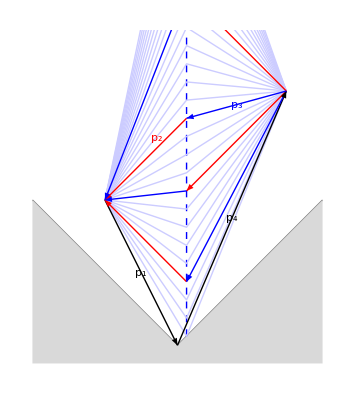

```mathematica
regular=Graphics[{
Gray,
Line[{{xmin,-xmin},{0,0},{xmax,xmax}}],
LightGray,
Polygon[{{xmin,-xmin},{0,0},{xmax,xmax},{xmax,ymin},{xmin,ymin}}],
Blue,
Dashed,
Line[{{qx,Abs[qx]},{qx,ymax}}],
Dashing[None],
RGBColor[{0.8,0.8,1}],
Table[Line[{p4,{qx,y},p1}],{y,DeleteElements[Table[y,{y,Abs[qx],1.5,1/20}],{qx1[[2]],qx2[[2]],qx3[[2]],qx4[[2]]}]}],
Black,Thick,
Arrow[{{0,0},p4}],
Arrow[{p1,{0,0}}],
Red,
Arrow[{p4,qx1}],
Arrow[{p4,qx2}],
Arrow[{qx3,p1}],
Arrow[{qx4,p1}],
Blue,
Arrow[{qx1,p1}],
Arrow[{qx2,p1}],
Arrow[{p4,qx3}],
Arrow[{p4,qx4}],
Black,
Text["p_4",0.5p4,{-2,0}],
Text["p_1",0.5p1,{2,0}],
Blue,
Text["p_3",0.5p4+0.5qx4,{0,-1.8}],
Red,
Text["p_2",0.3p1+0.7qx4,{1.5,-1.5}]
}//Flatten,PlotRange->{{xmin,xmax},{ymin,ymax}},BaseStyle->{FontSize->16,FontFamily->"Latin Modern Math"}]
```

### Export

```mathematica
SetDirectory[NotebookDirectory[]];
Export["figures/momenta_s.pdf",schannel]
Export["figures/momenta_t.pdf",tchannel]
Export["figures/momenta_regular.pdf",regular]
```

momenta_s.pdf

momenta_t.pdf

momenta_regular.pdf

### Animated diagrams

```mathematica
animated[x_]:=Table[Graphics[{
Gray,
Line[{{xmin,-xmin},{0,0},{xmax,xmax}}],
LightGray,
Polygon[{{xmin,-xmin},{0,0},{xmax,xmax},{xmax,ymin},{xmin,ymin}}],
Blue,
Dashed,
Line[{{x,Abs[x]},{x,ymax}}],
Dashing[None],
Black,Thick,
Arrow[{{0,0},p4}],
Arrow[{p1,{0,0}}],
Text["p_4",0.5p4,{-2,0}],
Text["p_1",0.5p1,{2,0}],
If[(p4[[1]]-x)^2==(p4[[2]]-y)^2,Red,Blue],
Arrow[{p4,{x,y}}],
Text["p_3",0.5p4+0.5{x,y},2{{0,1},{-1,0}}.Normalize[p4-{x,y}]],
If[(p1[[1]]-x)^2==(p1[[2]]-y)^2,Red,Blue],
Arrow[{{x,y},p1}],
Text["p_2",0.5p1+0.5{x,y},2{{0,-1},{1,0}}.Normalize[p1-{x,y}]]
}//Flatten,PlotRange->{{xmin,xmax},{ymin,ymax}},BaseStyle->{FontSize->16,FontFamily->"Latin Modern Math"}],{y,Abs[x],1,1/40}];
```

```mathematica
Export["figures/momenta_regular.gif",animated[qx],"DisplayDurations"->0.5]
```

momenta_regular.gif

```mathematica
Export["figures/momenta_s.gif",animated[sx],"DisplayDurations"->0.5]
```

momenta_s.gif

```mathematica
Export["figures/momenta_t.gif",animated[tx],"DisplayDurations"->0.5]
```

momenta_t.gif